## Wuschel-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

This is a Cellzilla2D example that is based on the "Activator" model in 
H Jonsson, M Heisler, GV Reddy, V Agrawal, V Gor, BE Shapiro, E Mjolsness & EM Meyerowitz (2005) "Modeling the organization of the WUSCHEL expression domain in the shoot apical meristem," Bioinformatics, Vol. 21 Suppl. 1, 2005, pages i232-i240.

For more details on the model see
http://bioinformatics.oxfordjournals.org/cgi/content/abstract/21/suppl_1/i232

This CPU times shown reflect a core-i7 920 CPU

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (8-Jan-2013)) loaded Wed 23 Jan 2013 19:18:10
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.92 (11-Nov-2012) loaded Wed 23 Jan 2013 19:18:14
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Define a cellular template to run the model on.

225 cells

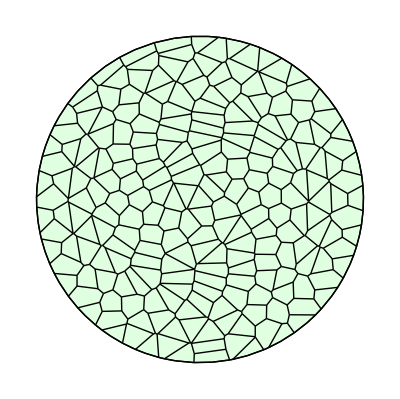

```mathematica
w=TemplateRandomCircularGrid[225,100];
Print[n=NTissueCells[w]," cells"];
ShowTissue[w]
```

Identify the "L1" layer - the cells on the outer boundary

```mathematica
L1Layer=CellsOnBoundary[w]
```

{170,175,176,177,178,179,180,181,182,183,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225}

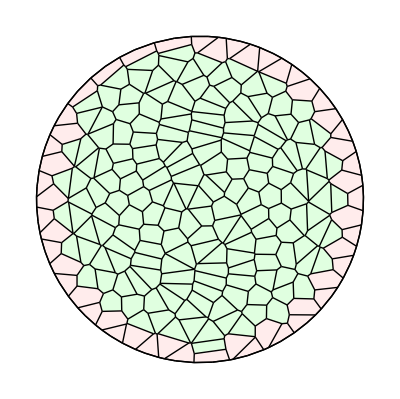

```mathematica
ShowTissueCells[w, L1Layer]
```

Define the Cellerator network that will produce the ODES as specified in the model

```mathematica
net={
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅,dw},{L1->Y+L1,ky},
{Y->∅,dy},
{∅⇄A,a,beta},
{A+Y->Y,d},
{2 A+B->3 A,c},
{A->B,b}};
```

Look at the ODES (without diffusion) in a single cell - this step is not required, it is for illustrative purposes only.

```mathematica
interpret[net][[1]]//TableForm
```

A'[t]==a-b A[t]-beta A[t]+c A[t]^2 B[t]-d A[t] Y[t]
B'[t]==b A[t]-c A[t]^2 B[t]
L1'[t]==0
W'[t]==-dw W[t]+(1+(hw+Twa A[t]+Twy Y[t])/(√(1+(hw+Twa A[t]+Twy Y[t])^2)))/(2 tauw)
Y'[t]==ky L1[t]-dy Y[t]

Define the initial conditions of all variables. 
Here we use zero for A,B, W, Y but that is not necessary.
L1 is an indicator function that must be 1 on the boundary and zero elsewhere.

```mathematica
ic[i_]:={A[i]->0,B[i]->0,W[i]->0,Y[i]->0,L1[i]->If[MemberQ[L1Layer,i],1,0]};
myic=Flatten[ic/@Range[n]];
```

Determine the large set of all Cellerator reactions in all cells, allowing A, B, and Y to diffuse with membrane penetrabilities DA, DB, and DY

```mathematica
cpu=TimeUsed[]; 
bignet=CelleratorNetwork[w, "Reactions"-> net,"Diffusion"-> {{A,DA},{B,DB},{Y,DY}}];
cpu=TimeUsed[]-cpu;
Print[cpu, " Seconds to generate network."];
```

225 Cells.

10 internal reactions in each cell.

2250 intracellular reactions.

3726 diffusion reactions.

5976 total reactions.

0.712045 Seconds to generate network.

Define the parameters for the model

```mathematica
parameters={d-> 2,DY-> 2,  Twy->-20,Twa->0.5,ky->0.2,kz->0.2,dy->0.1,dz->0.1,DZ->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,a->0.1,b->0.2,beta->0.1,c->0.1,DA->1.5,DB->15.0};
```

Rune a simulation using xlr8r

```mathematica
CPU=TimeUsed[];
sim=RunSim[bignet,parameters,myic,{0,1000}, MaxSteps-> 100000];
Print[TimeUsed[]-CPU," seconds to run the simulation"];
```

7.17245 seconds to run the simulation

Plot the results of a single variable

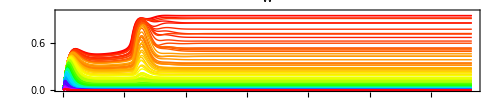

```mathematica
SimPlot[sim,W,{0,1000},PlotRange->{0,1},AspectRatio->.2,ImageSize->500,"Points"->300]
```

Plot the results for all variables

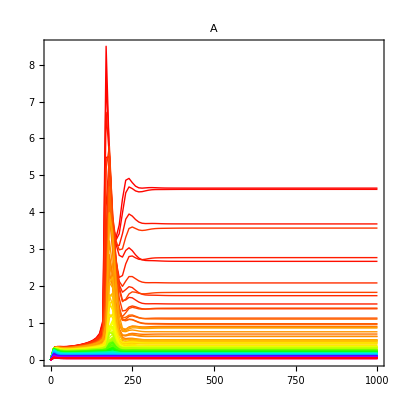
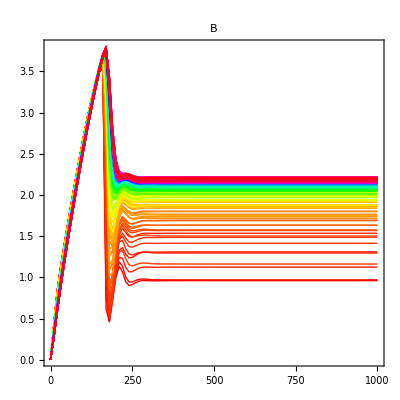
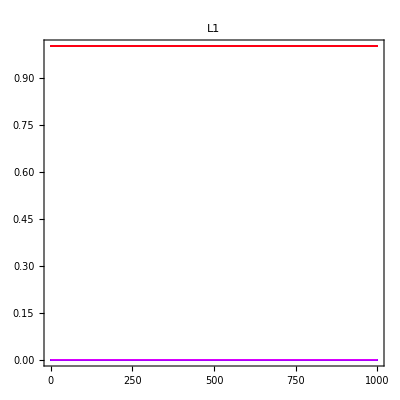
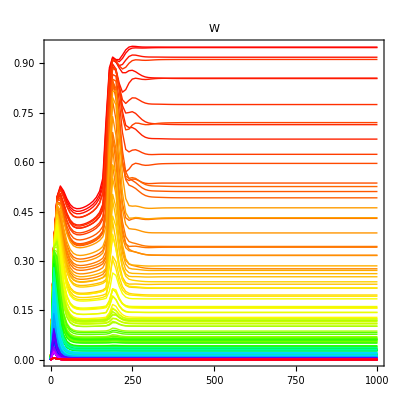
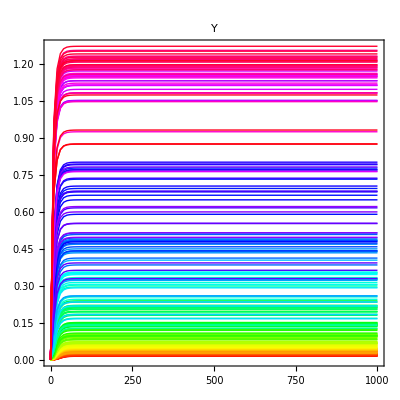

```mathematica
SimPlot[sim]
```

Use SimShowFinal to find the solution at the stop time of the simulation and automatically set the scales.

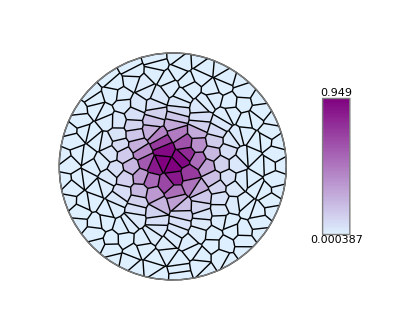

```mathematica
finalpic=SimShowFinal[sim,W,w,{LightBlue,Purple}]
```

SimShow allows you to look at the solution at at any time but does not show the scale bar.

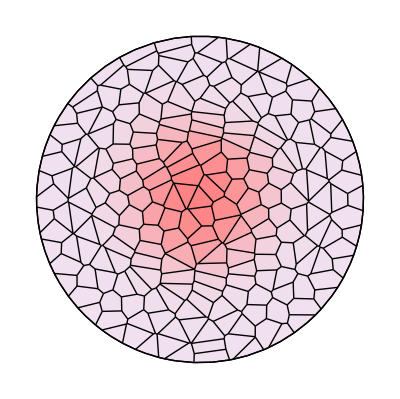

```mathematica
SimShow[sim,W, 50, w, {LightPurple, Pink}, {0, .5}]
```

SimShowAt will show the scale bar and autoscale the values.

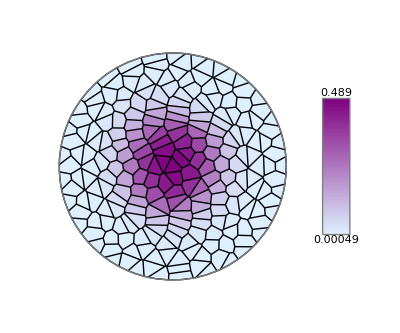

```mathematica
SimShowAt[sim, W, 50, w, {LightBlue, Purple}]
```

SimAnimate will produce a sequence of plots over time. If the start and stop time are the same only one plot will be returned.

This will generate a movie of the approach towards a steady state but it can only be viewed in Mathematica

```mathematica
m=SimAnimate[sim, W, w, {0,500, 50}, {LightGreen, Purple}, {0, 1}];
ListAnimate[m]
```

SaveFrames, ToMOV, ToAVI create higher resolution movie files.

If ffmpeg is not installed then only the JPG files will be saved and the movie will not actually be produced.

```mathematica
m=SimAnimate[sim, W, w, {0,400, 2}, {LightGreen, Purple}, {0, 1}];
```

```mathematica
SaveFrames[m, "JPG", 800, ".AVI", "Activator-Model"]
```